```mathematica
SetDirectory["~/Dropbox/Posttraumatic Medoids Disorder/CodeForPaper/"]
```

/Users/anellore/Dropbox/Posttraumatic Medoids Disorder/CodeForPaper

```mathematica
stretchText[char_,pos_,scale_,angle_: 0]:=Module[{g,coords,xMin,xMax,yMin,yMax},g=First@First@ImportString[ExportString[char,"PDF"],"TextOutlines"->True];
coords=Apply[Join,Cases[g,FilledCurve[___,p_]:>Flatten[p,1],Infinity]];
{{xMin,xMax},{yMin,yMax}}=Map[{Min[#],Max[#]}&[#]&,Transpose[coords]];
Rotate[Inset[Graphics[g,PlotRange->{{xMin,xMax},{yMin,yMax}},If[ListQ[scale],AspectRatio->Full,AspectRatio->Automatic]],pos,{xMin,yMin},scale],angle]]
```

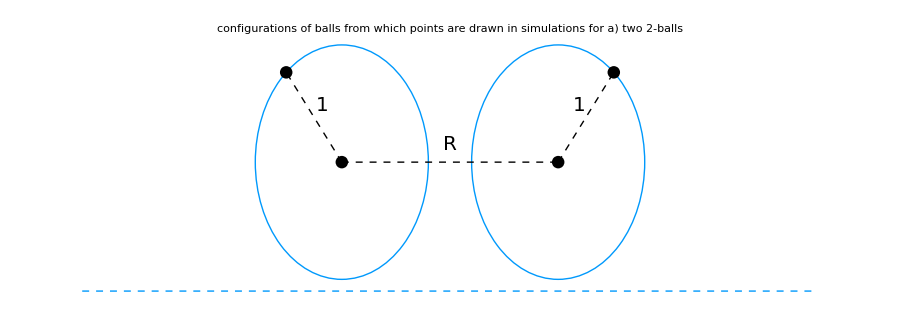

```mathematica
ballstwo=Show[Graphics[{RGBColor[0/256,154/256,253/256],Thick,Circle[{0,0}]}], Graphics[{RGBColor[0/256,154/256,253/256],Thick,Circle[{2.5, 0}]}], Graphics[{PointSize[.01],Point[{0,0}]}], Graphics[{PointSize[.01],Point[{2.5,0}]}],Graphics[{PointSize[.01],Point[{2.5+Cos[50 Degree],Sin[50 Degree]}]}],Graphics[{PointSize[.01],Point[{Cos[130 Degree],Sin[130 Degree]}]}],Graphics[{Dashed,Thick,Line[{{0,0}, {2.5,0}}]}], Graphics[{Text[Style["R", 20, FontFamily->"Futura"], {1.25,.15}]}],Graphics[{Dashed,Thick,Line[{{0,0}, {Cos[130 Degree],Sin[130 Degree]}}]}],Graphics[{Dashed,Thick,Line[{{2.5,0}, {2.5+Cos[50 Degree],Sin[50 Degree]}}]}], Graphics[{Text[Style["1", 20, FontFamily->"Futura"], {-.23,.48}]}],Graphics[{Text[Style["1", 20, FontFamily->"Futura"], {2.745,.48}]}], Graphics[{Dashed,RGBColor[0/256,154/256,253/256],Line[{{-3,-1.1}, {5.5,-1.1}}]}],PlotLabel->Grid[{{Style["configurations of balls from which points are drawn in simulations for", FontFamily->"Futura", FontSize->23]},{Style["a) two 2-balls", FontFamily->"Futura", FontColor->RGBColor[0/256,154/256,253/256], FontSize->391/15]}}], ImageSize->{900,320}]
```

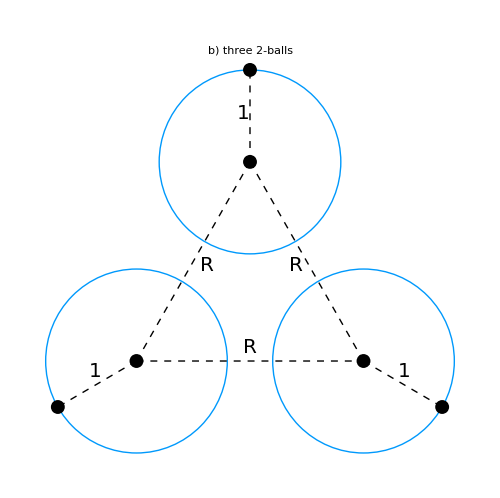

```mathematica
ballsthree=Show[Graphics[{RGBColor[0/256,154/256,253/256],Thick,Circle[{0,0}]}], Graphics[{RGBColor[0/256,154/256,253/256],Thick,Circle[{2.5, 0}]}], Graphics[{RGBColor[0/256,154/256,253/256],Thick,Circle[{2.5/2,2.5/2 * Sqrt[3]}]}],Graphics[{PointSize[.02],Point[{0,0}]}], Graphics[{PointSize[.02],Point[{2.5,0}]}],Graphics[{PointSize[.02],Point[{2.5/2,2.5/2*Sqrt[3]+1}]}],Graphics[{PointSize[.02],Point[{2.5/2,2.5/2 * Sqrt[3]}]}],Graphics[{PointSize[.02],Point[{2.5+Cos[-30 Degree],Sin[-30 Degree]}]}],Graphics[{PointSize[.02],Point[{Cos[210 Degree],Sin[210 Degree]}]}],Graphics[{Dashed,Thick,Line[{{0,0}, {2.5/2,2.5/2 * Sqrt[3]}}]}], Graphics[{Dashed,Thick,Line[{{0,0}, {2.5,0}}]}],Graphics[{Dashed,Thick,Line[{{2.5,0}, {2.5/2,2.5/2 * Sqrt[3]}}]}],Graphics[{Text[Style["R", 20, FontFamily->"Futura"], {1.25,.15}]}],Graphics[{Text[Style["R", 20, FontFamily->"Futura"], {.775,1.04}]}],Graphics[{Text[Style["R", 20, FontFamily->"Futura"], {1.761,1.04}]}],Graphics[{Dashed,Thick,Line[{{0,0}, {Cos[210 Degree],Sin[210 Degree]}}]}],Graphics[{Dashed,Thick,Line[{{2.5/2,2.5/2 * Sqrt[3]}, {2.5/2,2.5/2 * Sqrt[3]+1}}]}],Graphics[{Dashed,Thick,Line[{{2.5,0}, {2.5+Cos[-30 Degree],Sin[-30 Degree]}}]}], Graphics[{Text[Style["1", 20, FontFamily->"Futura"], {-.45,-.11}]}],Graphics[{Text[Style["1", 20, FontFamily->"Futura"], {2.945,-.11}]}],Graphics[{Text[Style["1", 20, FontFamily->"Futura"], {1.17,2.69}]}], PlotLabel->Style["b) three 2-balls", FontFamily->"Futura", FontColor->RGBColor[0/256,154/256,253/256], FontSize->391/15],ImageSize->{500,498}]
```

```mathematica
Export["diagramtop.pdf",ballstwo,"AllowRasterization"->True,ImageResolution->600]
```

diagramtop.pdf

```mathematica
Export["diagrambottom.pdf",ballsthree,"AllowRasterization"->True,ImageResolution->600]
```

diagrambottom.pdf